```mathematica
Table30=Table[{m/30,Length[IntegerPartitions[30,{m}]]/PartitionsP[30]}, {m,1,30}];
```

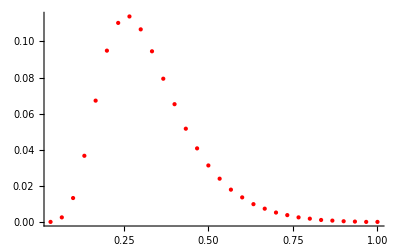

```mathematica
Fig30=ListPlot[Table30, PlotStyle->Red]
```

```mathematica
Table50=Table[{m/50,Length[IntegerPartitions[50,{m}]]/PartitionsP[50]}, {m,1,50}];
```

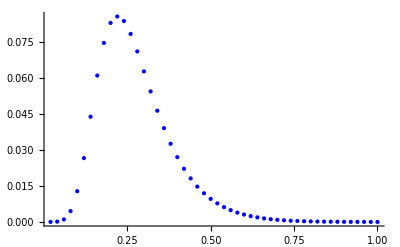

```mathematica
Fig50=ListPlot[Table50, PlotStyle->Blue]
```

```mathematica
Table70=Table[{m/70,Length[IntegerPartitions[70,{m}]]/PartitionsP[70]}, {m,1,70}];
```

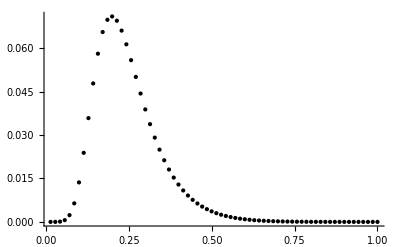

```mathematica
Fig70=ListPlot[Table70, PlotStyle->Black]
```

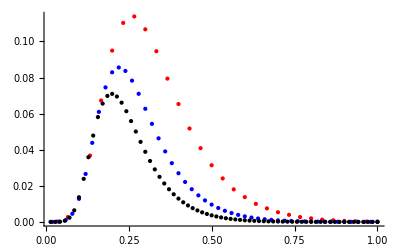

```mathematica
Show[Fig30,Fig50,Fig70]
```

```mathematica
Table30a=Table[{m/70,Length[IntegerPartitions[30,{m}]]/PartitionsP[30]}, {m,1,30}];
Table50a=Table[{m/70,Length[IntegerPartitions[50,{m}]]/PartitionsP[50]}, {m,1,50}];
Table70a=Table[{m/70,Length[IntegerPartitions[70,{m}]]/PartitionsP[70]}, {m,1,70}];
```

```mathematica
Fig30a=ListPlot[Table30a, PlotStyle->Red];
Fig50a=ListPlot[Table50a, PlotStyle->Black];
Fig70a=ListPlot[Table70a, PlotStyle->Blue];
```

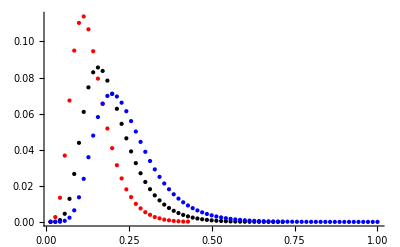

```mathematica
Show[Fig30a,Fig50a,Fig70a]
```

```mathematica
Hyperlink["Planck Distribution","http://hyperphysics.phy-astr.gsu.edu/hbase/mod6.html"]
```

```mathematica
ν^2 ν/(ⅇ^(ν/kT)-1)
```

```mathematica
Series[ν/(ⅇ^(ν/kT)-1),{ν,0,3}]
```

kT-ν/2+ν^2/(12 kT)+O[ν]^4

```mathematica
Manipulate[Plot[ν^2 ν/(ⅇ^(ν/kT)-1),{ν,.01,40}, PlotRange->{0,40}],{kT,1,3}]
```

```mathematica
D[ν^2 ν/(ⅇ^(ν/kT)-1),ν]//Simplify
```

(ν^2 (3 (-1+ⅇ^(ν/kT)) kT-ⅇ^(ν/kT) ν))/((-1+ⅇ^(ν/kT))^2 kT)

```mathematica
3(ⅇ^x-1)-x ⅇ^x
```